```mathematica
Quit[]
```

#### Get component function (temporary)

```mathematica
Needs["Olveretal`"];
ClearAll[GetComponent]
Options[GetComponent]={Coordinates->"Spherical",Mute->True};
GetComponent[solvec_List,expr_List,layer_Integer,layout_List,n_Integer,OptionsPattern[]]:=
Block[{position,subdomain,nsubdomains,partition,zeroInDomain,startindex,listParity,listExtracted,(*options*) coordinates},

(* set up options *)
coordinates=OptionValue[Coordinates];
If[!OptionValue[Mute],
If[SameQ[coordinates,"Spheroidal"],Print["Spheroidal coordinates"],Print["Spherical coordinates"]]
];

(* recover subdomains from model *)
partition=Partition[Sort(*@Rest*)[Fennec`domain],2,1];
nsubdomains=Length[partition];
Table[subdomain[i]=partition⟦i⟧,{i,1,Length[partition]}];
If[SameQ[N@First[subdomain[1]],0.],zeroInDomain=True,zeroInDomain=False];

(* find component position in solution vector *)
position=Flatten@Position[layout,Alternatives@@expr];

(* find parity of fields accross the origin based on their indices of spherical harmonics *)
listParity=
Block[{out},
If[zeroInDomain&&SameQ[layer,1],
Which[
SameQ[coordinates,"Spheroidal"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ+𝓂]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ+𝓂]],out="odd";,
True,Print["error with parity !"]
],
SameQ[coordinates,"Spherical"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ]],out="odd";,
True,Print["error with parity !"];
],
True,Print["error with coordinates !"];
]
];
out
]&/@expr;

(* extracted elements from solution vector *)
listExtracted=
Block[{extracted},
If[zeroInDomain,
startindex=Max[(layer-3/2)*n*Length[layout]+1,1];
If[SameQ[layer,1],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n/2-1⟧,{(#-1)*n/2+1,#*n/2}],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
],
startindex=(layer-1)*n*Length[layout]+1;
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
]
]&/@position;

(* output: riffle with zeroes if zero is in first layer *)
If[zeroInDomain&&SameQ[layer,1],
Table[
Switch[listParity⟦i⟧,
"even",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ],
"odd",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ,{1,-1,2}],
True,Print["error with Riffle !"]
]
,{i,1,Length[expr]}],
N@listExtracted
]

]
```

Get::noopen: Cannot open Olveretal`.

Needs::nocont: Context Olveretal` was not created when Needs was evaluated.

# Inviscid Navier-Stokes + axial magnetic field

## Load fennec & spectral package

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["spectral`","../spectral.m"];
Needs["fennec`","../fennec.m"];
```

## Components of vorticity and thermal equations

### two curls

```mathematica
rCurlCurlInertia[ℓ_,𝓂_]:=(ℓ^2 (1+ℓ)^2 P[ℓ,𝓂][r])/r^2-(2 ℓ (1+ℓ) P[ℓ,𝓂]'[r])/r-ℓ (1+ℓ) P[ℓ,𝓂]''[r];
rCurlCurlCoriolis[ℓ_,𝓂_]:=2(-(ℓ (1+2 ℓ) (-√((ℓ (-1+ℓ^2))/(-1+4 ℓ^2))+√((1-ℓ^2)/(ℓ-4 ℓ^3))) √(-((-1+ℓ^2) (ℓ-𝓂) (ℓ+𝓂))/(ℓ-4 ℓ^3)) T[-1+ℓ,𝓂][r])/r-ℓ (1+2 ℓ) √((1-ℓ^2)/(ℓ-4 ℓ^3)) √(-((-1+ℓ^2) (ℓ-𝓂) (ℓ+𝓂))/(ℓ-4 ℓ^3)) T[-1+ℓ,𝓂]'[r]-(ⅈ ℓ (1+ℓ) 𝓂 P[ℓ,𝓂][r])/r^2+(2 ⅈ 𝓂 P[ℓ,𝓂]'[r])/r+ⅈ 𝓂 P[ℓ,𝓂]''[r]-((1+ℓ) (1+2 ℓ) (√((ℓ (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3))+√((ℓ (1+ℓ) (2+ℓ))/(3+4 ℓ (2+ℓ)))) √((ℓ (2+ℓ) (1+ℓ-𝓂) (1+ℓ+𝓂))/((1+ℓ) (1+2 ℓ) (3+2 ℓ))) T[1+ℓ,𝓂][r])/r-(1+ℓ) (1+2 ℓ) √((ℓ (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3)) √((ℓ (2+ℓ) (1+ℓ-𝓂) (1+ℓ+𝓂))/((1+ℓ) (1+2 ℓ) (3+2 ℓ))) T[1+ℓ,𝓂]'[r]);
```

```mathematica
(*(* axial field *)
ClearAll[rCurlCurlLorentzForce]
rCurlCurlLorentzForce[ℓ_,𝓂_]:=-1/r^3(-ℓ (1+2 ℓ) (√((ℓ (-1+ℓ^2))/(-1+4 ℓ^2))-√((ℓ^5 (-1+ℓ^2))/(-1+4 ℓ^2))) √(((1-ℓ^2) (ℓ-𝓂) (ℓ+𝓂))/(ℓ-4 ℓ^3)) F[-1+ℓ,𝓂][r]+(1+ℓ) (1+2 ℓ) (2 √((ℓ (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3))+√((ℓ^5 (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3))-2 √((ℓ (1+ℓ) (2+ℓ))/(3+4 ℓ (2+ℓ)))-√((ℓ^5 (1+ℓ) (2+ℓ))/(3+4 ℓ (2+ℓ)))+3 ℓ (√((ℓ (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3))-√((ℓ (1+ℓ) (2+ℓ))/(3+4 ℓ (2+ℓ))))) √((ℓ (2+ℓ) (1+ℓ-𝓂) (1+ℓ+𝓂))/((1+ℓ) (1+2 ℓ) (3+2 ℓ))) F[1+ℓ,𝓂][r]-ⅈ r ℓ (1+ℓ) 𝓂 G[ℓ,𝓂][r]-r ℓ (1+ℓ) (1+2 ℓ) √((ℓ (-1+ℓ^2))/(-1+4 ℓ^2)) √(((1-ℓ^2) (ℓ-𝓂) (ℓ+𝓂))/(ℓ-4 ℓ^3)) F[-1+ℓ,𝓂]'[r]-r (1+ℓ) (1+2 ℓ) (2 √((ℓ (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3))+3 ℓ √((ℓ (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3))+√((ℓ^5 (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3))-2 √((ℓ (1+ℓ) (2+ℓ))/(3+4 ℓ (2+ℓ)))) √((ℓ (2+ℓ) (1+ℓ-𝓂) (1+ℓ+𝓂))/((1+ℓ) (1+2 ℓ) (3+2 ℓ))) F[1+ℓ,𝓂]'[r]+2 ⅈ r^2 𝓂 G[ℓ,𝓂]'[r]-r^2 ℓ (1+2 ℓ) (√((ℓ (-1+ℓ^2))/(-1+4 ℓ^2))-3 √((1-ℓ^2)/(ℓ-4 ℓ^3))) √(((1-ℓ^2) (ℓ-𝓂) (ℓ+𝓂))/(ℓ-4 ℓ^3)) F[-1+ℓ,𝓂]''[r]+r^2 (1+ℓ) (1+2 ℓ) (3 √((ℓ (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3))+√((ℓ (1+ℓ) (2+ℓ))/(3+4 ℓ (2+ℓ)))) √((ℓ (2+ℓ) (1+ℓ-𝓂) (1+ℓ+𝓂))/((1+ℓ) (1+2 ℓ) (3+2 ℓ))) F[1+ℓ,𝓂]''[r]+ⅈ r^3 𝓂 G[ℓ,𝓂]''[r]+r^3 ℓ (1+2 ℓ) √((1-ℓ^2)/(ℓ-4 ℓ^3)) √(((1-ℓ^2) (ℓ-𝓂) (ℓ+𝓂))/(ℓ-4 ℓ^3)) F[-1+ℓ,𝓂]'''[r]+r^3 (1+ℓ) (1+2 ℓ) √((ℓ (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3)) √((ℓ (2+ℓ) (1+ℓ-𝓂) (1+ℓ+𝓂))/((1+ℓ) (1+2 ℓ) (3+2 ℓ))) F[1+ℓ,𝓂]'''[r]);*)
```

```mathematica
(* Malkus field *)
ClearAll[rCurlCurlLorentzForce]
rCurlCurlLorentzForce[ℓ_,𝓂_]:=(ⅈ ℓ (1+ℓ) (-2+ℓ+ℓ^2) 𝓂 F[ℓ,𝓂][r])/r^2+(2 (-1+ℓ)^2 (1+ℓ) √((ℓ-𝓂) (ℓ+𝓂)) G[-1+ℓ,𝓂][r])/(r (-1+2 ℓ))-(2 ℓ (2+ℓ)^2 √((1+ℓ-𝓂) (1+ℓ+𝓂)) G[1+ℓ,𝓂][r])/(r (3+2 ℓ))-(2 ⅈ (-2+ℓ+ℓ^2) 𝓂 F[ℓ,𝓂]'[r])/r-(2 (-1+ℓ^2) √((ℓ-𝓂) (ℓ+𝓂)) G[-1+ℓ,𝓂]'[r])/(-1+2 ℓ)-(2 ℓ (2+ℓ) √((1+ℓ-𝓂) (1+ℓ+𝓂)) G[1+ℓ,𝓂]'[r])/(3+2 ℓ)-ⅈ (-2+ℓ+ℓ^2) 𝓂 F[ℓ,𝓂]''[r];
```

### one curl

```mathematica
rCurlInertia[ℓ_,𝓂_]:=ℓ (1+ℓ) T[ℓ,𝓂][r];
rCurlCoriolis[ℓ_,𝓂_]:=2(((-1+ℓ)^2 (1+ℓ) √((ℓ-𝓂) (ℓ+𝓂)) P[-1+ℓ,𝓂][r])/(r (-1+2 ℓ))-((-1+ℓ^2) √((ℓ-𝓂) (ℓ+𝓂)) P[-1+ℓ,𝓂]'[r])/(-1+2 ℓ)-(ℓ (2+ℓ)^2 √((1+ℓ-𝓂) (1+ℓ+𝓂)) P[1+ℓ,𝓂][r])/(r (3+2 ℓ))-(ℓ (2+ℓ) √((1+ℓ-𝓂) (1+ℓ+𝓂)) P[1+ℓ,𝓂]'[r])/(3+2 ℓ)-ⅈ 𝓂 T[ℓ,𝓂][r]);
```

```mathematica
(*(* axial field *)
ClearAll[rCurlLorentzForce]
rCurlLorentzForce[ℓ_,𝓂_]:=(ⅈ ℓ (1+ℓ) 𝓂 F[ℓ,𝓂][r])/r^2-((-1+ℓ)^2 (1+ℓ) √(ℓ^2-𝓂^2) G[-1+ℓ,𝓂][r])/(r (-1+2 ℓ))+(ℓ (2+ℓ)^2 √((1+ℓ-𝓂) (1+ℓ+𝓂)) G[1+ℓ,𝓂][r])/(r (3+2 ℓ))-(2 ⅈ 𝓂 F[ℓ,𝓂]'[r])/r+((-1+ℓ^2) √(ℓ^2-𝓂^2) G[-1+ℓ,𝓂]'[r])/(-1+2 ℓ)+(ℓ (2+ℓ) √((1+ℓ-𝓂) (1+ℓ+𝓂)) G[1+ℓ,𝓂]'[r])/(3+2 ℓ)-ⅈ 𝓂 F[ℓ,𝓂]''[r];*)
```

```mathematica
(* Malkus field *)
ClearAll[rCurlLorentzForce]
rCurlLorentzForce[ℓ_,𝓂_]:=ⅈ (-1+ℓ) (2+ℓ) 𝓂 G[ℓ,𝓂][r]+(2 (-1+ℓ^2) √((ℓ-𝓂) (ℓ+𝓂)) ((-1+ℓ) F[-1+ℓ,𝓂][r]-r F[-1+ℓ,𝓂]'[r]))/(r (-1+2 ℓ))-(2 ℓ (2+ℓ) √((1+ℓ-𝓂) (1+ℓ+𝓂)) ((2+ℓ) F[1+ℓ,𝓂][r]+r F[1+ℓ,𝓂]'[r]))/(r (3+2 ℓ))
```

### induction equation (uniform field)

```mathematica
(*ClearAll[rb,rCurlb,rCurlCurlb,rInduction,rCurlInduction]
rb[ℓ_,𝓂_]:=ℓ (1+ℓ) F[ℓ,𝓂][r];
rCurlb[ℓ_,𝓂_]:=ℓ (1+ℓ) G[ℓ,𝓂][r];
rCurlCurlb[ℓ_,𝓂_]:=-ℓ (1+ℓ) (-(ℓ (1+ℓ) F[ℓ,𝓂][r])/r^2+(2 F[ℓ,𝓂]'[r])/r+F[ℓ,𝓂]''[r]);
rInduction[ℓ_,𝓂_]:=((-1+ℓ)^2 (1+ℓ) √((ℓ-𝓂) (ℓ+𝓂)) P[-1+ℓ,𝓂][r])/(r (-1+2 ℓ))-(ℓ (2+ℓ)^2 √((1+ℓ-𝓂) (1+ℓ+𝓂)) P[1+ℓ,𝓂][r])/(r (3+2 ℓ))-ⅈ 𝓂 T[ℓ,𝓂][r]-((-1+ℓ^2) √((ℓ-𝓂) (ℓ+𝓂)) P[-1+ℓ,𝓂]'[r])/(-1+2 ℓ)-(ℓ (2+ℓ) √((1+ℓ-𝓂) (1+ℓ+𝓂)) P[1+ℓ,𝓂]'[r])/(3+2 ℓ);
rOhmic[ℓ_,𝓂_]:=ℓ (1+ℓ) (-(ℓ (1+ℓ) F[ℓ,𝓂][r])/r^2+(2 F[ℓ,𝓂]'[r])/r+F[ℓ,𝓂]''[r]);
rCurlInduction[ℓ_,𝓂_]:=-(ⅈ ℓ (1+ℓ) 𝓂 P[ℓ,𝓂][r])/r^2+((-1+ℓ)^2 (1+ℓ) √((ℓ-𝓂) (ℓ+𝓂)) T[-1+ℓ,𝓂][r])/(r (-1+2 ℓ))-(ℓ (2+ℓ)^2 √((1+ℓ-𝓂) (1+ℓ+𝓂)) T[1+ℓ,𝓂][r])/(r (3+2 ℓ))+(2 ⅈ 𝓂 P[ℓ,𝓂]'[r])/r-((-1+ℓ^2) √((ℓ-𝓂) (ℓ+𝓂)) T[-1+ℓ,𝓂]'[r])/(-1+2 ℓ)-(ℓ (2+ℓ) √((1+ℓ-𝓂) (1+ℓ+𝓂)) T[1+ℓ,𝓂]'[r])/(3+2 ℓ)+ⅈ 𝓂 P[ℓ,𝓂]''[r];
rCurlOhmic[ℓ_,𝓂_]:=-(ℓ^2 (1+ℓ)^2 G[ℓ,𝓂][r])/r^2+(2 ℓ (1+ℓ) G[ℓ,𝓂]'[r])/r+ℓ (1+ℓ) G[ℓ,𝓂]''[r];
rCurlCurlInduction[ℓ_,𝓂_]:=1/(r^3 (-3+4 ℓ+4 ℓ^2))ℓ ((3+2 ℓ) (-1+ℓ^2)^2 √(ℓ^2-𝓂^2) P[-1+ℓ,𝓂][r]-ℓ (2+ℓ)^2 (-1+ℓ+2 ℓ^2) √(1+2 ℓ+ℓ^2-𝓂^2) P[1+ℓ,𝓂][r]-ⅈ r (-3+ℓ+8 ℓ^2+4 ℓ^3) 𝓂 T[ℓ,𝓂][r])-((-1+ℓ) ℓ (1+ℓ)^2 √(ℓ^2-𝓂^2) P[-1+ℓ,𝓂]'[r])/(r^2 (-1+2 ℓ))-(ℓ^2 (2+3 ℓ+ℓ^2) √(1+2 ℓ+ℓ^2-𝓂^2) P[1+ℓ,𝓂]'[r])/(r^2 (3+2 ℓ))+(2 ⅈ 𝓂 T[ℓ,𝓂]'[r])/r+((-3+ℓ+3 ℓ^2-ℓ^3) √(ℓ^2-𝓂^2) P[-1+ℓ,𝓂]''[r])/(r (-1+2 ℓ))+(ℓ (8+6 ℓ+ℓ^2) √(1+2 ℓ+ℓ^2-𝓂^2) P[1+ℓ,𝓂]''[r])/(r (3+2 ℓ))+ⅈ 𝓂 T[ℓ,𝓂]''[r]+((-1+ℓ^2) √(ℓ^2-𝓂^2) P[-1+ℓ,𝓂]'''[r])/(-1+2 ℓ)+(ℓ (2+ℓ) √(1+2 ℓ+ℓ^2-𝓂^2) P[1+ℓ,𝓂]'''[r])/(3+2 ℓ);
rCurlCurlOhmic[ℓ_,𝓂_]:=-1/r^4ℓ (1+ℓ) (ℓ (-2-ℓ+2 ℓ^2+ℓ^3) F[ℓ,𝓂][r]+r^2 (-2 ℓ (1+ℓ) F[ℓ,𝓂]''[r]+r (4 F[ℓ,𝓂]'''[r]+r F[ℓ,𝓂]''''[r])));*)
```

### induction equation (Malkus field)

```mathematica
ClearAll[rb,rCurlb,rCurlCurlb,rInduction,rCurlInduction]
rb[ℓ_,𝓂_]:=ℓ (1+ℓ) F[ℓ,𝓂][r];
rCurlb[ℓ_,𝓂_]:=ℓ (1+ℓ) G[ℓ,𝓂][r];
rCurlCurlb[ℓ_,𝓂_]:=-ℓ (1+ℓ) (-(ℓ (1+ℓ) F[ℓ,𝓂][r])/r^2+(2 F[ℓ,𝓂]'[r])/r+F[ℓ,𝓂]''[r]);
rInduction[ℓ_,𝓂_]:=-ⅈ ℓ (1+ℓ) 𝓂 P[ℓ,𝓂][r]
rCurlInduction[ℓ_,𝓂_]:=-ⅈ ℓ (1+ℓ) 𝓂 T[ℓ,𝓂][r]
```

### putting things together

```mathematica
Le2=1/100;η=0.0;
```

```mathematica
ClearAll[eqNS1,eqNS2,eqInduction1,eqInduction2]
eqNS1[ℓ_,𝓂_]:=(ⅈ ω)rCurlCurlInertia[ℓ,𝓂]+rCurlCurlCoriolis[ℓ,𝓂]-Le2 rCurlCurlLorentzForce[ℓ,𝓂]==0
eqNS2[ℓ_,𝓂_]:=(ⅈ ω)rCurlInertia[ℓ,𝓂]+rCurlCoriolis[ℓ,𝓂]-Le2 rCurlLorentzForce[ℓ,𝓂]==0
eqInduction1[ℓ_,𝓂_]:=(ⅈ ω)rb[ℓ,𝓂]+ rInduction[ℓ,𝓂]==0
(*eqInduction1[ℓ_,𝓂_]:=(ⅈ ω)rCurlCurlb[ℓ,𝓂]+ rCurlCurlInduction[ℓ,𝓂]==0*)
eqInduction2[ℓ_,𝓂_]:=(ⅈ ω)rCurlb[ℓ,𝓂]+ rCurlInduction[ℓ,𝓂]==0
```

## Call to fennec

```mathematica
With[{𝓂=1,ℓmax=6},
ℒ=Flatten@Table[Simplify[{eqNS1[ℓ,𝓂],eqNS2[ℓ-1,𝓂],eqInduction1[ℓ,𝓂],eqInduction2[ℓ-1,𝓂]}],{ℓ,2,ℓmax,2}];
(*ℒ=Flatten@Table[Simplify[{eqNS1[ℓ,𝓂],eqNS2[ℓ-1,𝓂],eqInduction1[ℓ-1,𝓂],eqInduction2[ℓ,𝓂]}],{ℓ,2,ℓmax,2}];*)
ℬ=Flatten@Table[{P[ℓ,𝓂][1]==0(*,F[ℓ,𝓂]'[1]+(ℓ+1)F[ℓ,𝓂][1]==0*)},{ℓ,2,ℓmax,2}];
(*ℬ=Flatten@Table[{P[ℓ,𝓂][1]==0,F[ℓ-1,𝓂]'[1]+((ℓ-1)+1)F[ℓ-1,𝓂][1]==0,G[ℓ,𝓂][1]==0},{ℓ,2,ℓmax,2}];*)
𝒱=SortBy[Flatten@Table[{P[ℓ,𝓂],T[ℓ-1,𝓂],F[ℓ,𝓂],G[ℓ-1,𝓂]},{ℓ,2,ℓmax,2}],Head]
(*𝒱=SortBy[Flatten@Table[{P[ℓ,𝓂],T[ℓ-1,𝓂],F[ℓ-1,𝓂],G[ℓ,𝓂]},{ℓ,2,ℓmax,2}],Head]*)
];
```

```mathematica
A=FennecFun[Join[ℒ,ℬ],𝒱,{r,0,1},40,eigenvalue->ω]
```

partition of the spatial domain : {{0,1}}

regularity conditions will be enforced at r=0 based on indices of spherical harmonics

eigenvalue problem of type :  (A0+A1 ω)x==0

Size of output matrices : 240x240

{SparseArray[…],SparseArray[…]}

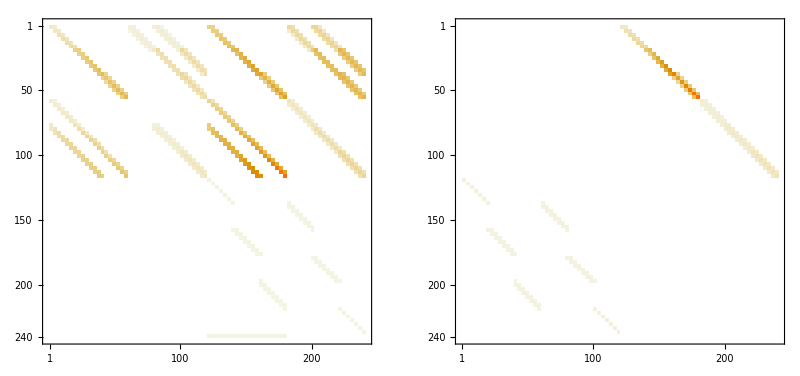

```mathematica
GraphicsRow[MatrixPlot/@Abs[A]]
```

## Solve and post-process

```mathematica
(*target=(*1.306078;*)(*0.611984935*)1;*)
target=0.637279714560192
```

0.63728

```mathematica
{eig,eigv}=Sort@Eigensystem[{A⟦1⟧,-A⟦2⟧}]//Chop;
eigv=Delete[eigv,Position[eig,ComplexInfinity]];
eig=Delete[eig,Position[eig,ComplexInfinity]];
pos=Nearest[eig->Automatic,target,1][[1]];
```

```mathematica
eig⟦pos⟧
eigv⟦pos⟧;
```

0.618261

```mathematica
(* extract components from solution *)
ClearAll[out,outnull]
Block[{list,coef,assoc=<||>},
Table[
list[layer]=Fennec`layout⟦layer⟧;
coef[layer]=Chop@GetComponent[eigv⟦pos⟧,list[layer],layer,Fennec`layout⟦layer⟧,Fennec`nr];
AppendTo[assoc,AssociationThread[list[layer],coef[layer]]]
,{layer,1,Fennec`nlayers}];
out=assoc;
]
outnull=Map[(#)->ConstantArray[0,Fennec`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ-1,𝓂]]~Join~Map[(#)->ConstantArray[0,Fennec`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ+1,𝓂]];
AppendTo[out,outnull];
```

```mathematica
ClearAll[NChebevalC]
NChebevalC[c_][x_]:=NChebeval[N[Re[c]]][x]+ⅈ NChebeval[N[Im[c]]][x]
xk=Cos[((2Range[1,Fennec`nr]-1)π)/(2Fennec`nr)]//N;
rk=Fennec`rfu[1][xk];
```

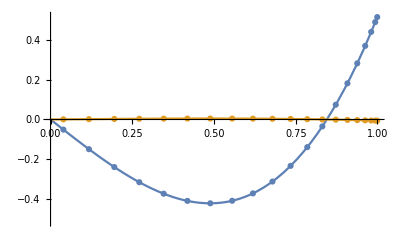

```mathematica
(* plot chosen component *)
data=NChebevalC[T[1,1]/.out][rk];
interp=Interpolation[{rk,data}ᵀ];
Show[Plot[{Re[interp[r]],Im[interp[r]]},{r,0,1},PlotRange->{{0,1},All}],ListPlot[{{rk,Re[data]}ᵀ,{rk,Im[data]}ᵀ}]]
```

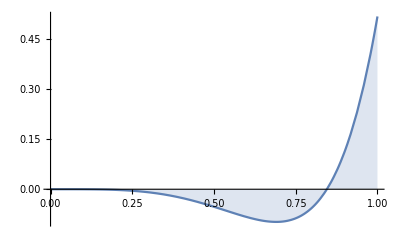

-0.000159627

```mathematica
(* Compute angular momentum *)
dataAM=rk^3 NChebevalC[T[1,1]/.out][rk];
interpAM=Interpolation[{rk,dataAM}ᵀ];
Plot[Re[interpAM[r]],{r,0,1},Filling->Axis,PlotRange->All]
8/3 π NIntegrate[Re[interpAM[r]],{r,0,1}]
```

```mathematica
(* Not working atm *)
(*(* Compute angular momentum *)
r3ck=NChebckf[r^3,r,Fennec`nr];
TimesCheb[r3ck,T[1,1]/.out];
I0Cheb[%,{0,1}]*)
```

## Plot fields

```mathematica
ClearAll[up,ut,upint,utint,urint,ucint,upintconj,ucintconj,urintconj,utintconj,uout]
ClearAll[bp,bt,bpint,btint,brint,bcint,bpintconj,bcintconj,brintconj,btintconj,bout]
gridr=N@Subdivide[Sequence@@Fennec`layer[1],100];
Block[{mode=pos,ℓ,𝓂,head,subset=Fennec`layout⟦1⟧,listcomp,comp},
listcomp=GetComponent[(*solution*)eigv⟦mode⟧,subset,1,Fennec`layout⟦1⟧,Fennec`nr,Coordinates->"Spherical"];
Table[
head=Head[subset⟦i⟧];ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
comp=listcomp⟦i⟧;
Which[
SameQ[head,P],
up[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Fennec`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Fennec`ufr[1][x]])]/@gridr)&@comp);
upint[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]}ᵀ];
upintconj[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]*}ᵀ];
urint[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upint[ℓ,𝓂][#]]&;
urintconj[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upintconj[ℓ,𝓂][#]]&;
ucint[ℓ,𝓂]=Evaluate[(upint[ℓ,𝓂][#])/#+upint[ℓ,𝓂]'[#]]&;
ucintconj[ℓ,𝓂]=Evaluate[(upintconj[ℓ,𝓂][#])/#+upintconj[ℓ,𝓂]'[#]]&,
SameQ[head,T],
ut[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Fennec`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Fennec`ufr[1][x]])]/@gridr)&@comp);
utint[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]}ᵀ];
utintconj[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]*}ᵀ],
SameQ[head,F],
bp[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Fennec`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Fennec`ufr[1][x]])]/@gridr)&@comp);
bpint[ℓ,𝓂]=Interpolation[{gridr,bp[ℓ,𝓂]}ᵀ];
bpintconj[ℓ,𝓂]=Interpolation[{gridr,bp[ℓ,𝓂]*}ᵀ];
brint[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# bpint[ℓ,𝓂][#]]&;
brintconj[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# bpintconj[ℓ,𝓂][#]]&;
bcint[ℓ,𝓂]=Evaluate[(bpint[ℓ,𝓂][#])/#+bpint[ℓ,𝓂]'[#]]&;
bcintconj[ℓ,𝓂]=Evaluate[(bpintconj[ℓ,𝓂][#])/#+bpintconj[ℓ,𝓂]'[#]]&,
SameQ[head,G],
bt[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Fennec`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Fennec`ufr[1][x]])]/@gridr)&@comp);
btint[ℓ,𝓂]=Interpolation[{gridr,bt[ℓ,𝓂]}ᵀ];
btintconj[ℓ,𝓂]=Interpolation[{gridr,bt[ℓ,𝓂]*}ᵀ]
];
(*dissipation[ℓ,𝓂]=Evaluate[1/2(4π)/(2ℓ+1)Ek(ℓ(ℓ+1)Abs[urint[ℓ,𝓂][#]+# ucint[ℓ,𝓂]'[#]-ucint[ℓ,𝓂][#]]^2+ℓ(ℓ+1)Abs[# utint[ℓ,𝓂]'[#]- utint[ℓ,𝓂][#]]^2+3 Abs[# urint[ℓ,𝓂]'[#]]^2+(ℓ-1)ℓ(ℓ+1)(ℓ+2)(Abs[ucint[ℓ,𝓂][#]]^2+Abs[utint[ℓ,𝓂][#]]^2))/.parameters]&;*)

uout[-1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]-ⅈ utint[ℓ,𝓂][#])]&;uout[0][ℓ,𝓂]=Evaluate[urint[ℓ,𝓂][#]]&;uout[+1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]+ⅈ utint[ℓ,𝓂][#])]&;
bout[-1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(bcint[ℓ,𝓂][#]-ⅈ btint[ℓ,𝓂][#])]&;bout[0][ℓ,𝓂]=Evaluate[brint[ℓ,𝓂][#]]&;bout[+1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(bcint[ℓ,𝓂][#]+ⅈ btint[ℓ,𝓂][#])]&;

,{i,1,Length[subset]}]
];
```

```mathematica
utint[ℓ_,𝓂_][r_]:=0;
urint[ℓ_,𝓂_][r_]:=0;
ucint[ℓ_,𝓂_][r_]:=0;
upint[ℓ_,𝓂_][r_]:=0;
utintconj[ℓ_,𝓂_][r_]:=0;
urintconj[ℓ_,𝓂_][r_]:=0;
ucintconj[ℓ_,𝓂_][r_]:=0;
upintconj[ℓ_,𝓂_][r_]:=0;
btint[ℓ_,𝓂_][r_]:=0;
brint[ℓ_,𝓂_][r_]:=0;
bcint[ℓ_,𝓂_][r_]:=0;
bpint[ℓ_,𝓂_][r_]:=0;
btintconj[ℓ_,𝓂_][r_]:=0;
brintconj[ℓ_,𝓂_][r_]:=0;
bcintconj[ℓ_,𝓂_][r_]:=0;
bpintconj[ℓ_,𝓂_][r_]:=0;
```

```mathematica
ClearAll[Y]
Y[ℓ_,𝓂_,θ_,ϕ_]:=Y[ℓ,𝓂,θ,ϕ]=√((4π)/(2 ℓ+1))SphericalHarmonicY[ℓ,𝓂,θ,ϕ]
```

```mathematica
gridθ=Range[0.,π,π/100];
Block[{ℓ,𝓂,subset=Fennec`layout⟦1⟧,ϕ=0},
gridur=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
Re@Which[
SameQ[{ℓ,𝓂},{0,0}],uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
SameQ[𝓂,0],uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
True,2*uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ]
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
griduθ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Re@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
griduϕ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Re@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
gridbr=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
Re@Which[
SameQ[{ℓ,𝓂},{0,0}],bout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
SameQ[𝓂,0],bout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
True,2*bout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ]
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
gridbθ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Re@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],bout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(bout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-bout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
gridbϕ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Re@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],bout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+bout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(bout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+bout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
];
griduρ=(gridurᵀ*Sin[gridθ]+griduθᵀ*Cos[gridθ])ᵀ;
griduz=(gridurᵀ*Cos[gridθ]-griduθᵀ*Sin[gridθ])ᵀ;
gridbρ=(gridbrᵀ*Sin[gridθ]+gridbθᵀ*Cos[gridθ])ᵀ;
gridbz=(gridbrᵀ*Cos[gridθ]-gridbθᵀ*Sin[gridθ])ᵀ;
```

```mathematica
coord[r_,θ_,ϕ_]:=
{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ] };
ClearAll[StreamMeridPlot,MeridPlot]
StreamMeridPlot[rj_List,θk_List,ϕ_,{v1_,v2_,s_},opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab,max=If[Max@Abs[s]≠0,Max@Abs[s],1]},
tab=Flatten[Table[{{√((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧},{{v1⟦j,k⟧,v2⟦j,k⟧},s⟦j,k⟧}},{j,1,nr},{k,1,nθ}],1];
tab;
ListStreamDensityPlot[tab,ColorFunction->(Lighter[ColorData["ThermometerColors"][Rescale[#,{-max,max} ]],0.1]&),ColorFunctionScaling->False,opts]]
coord[r_,θ_,ϕ_]:=
{Abs[r] Cos[ϕ] Sin[θ],Abs[r] Sin[θ] Sin[ϕ],Abs[r] Cos[θ] };
MeridPlot[rj_List,θk_List,mat_,ϕ_,opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab,max=If[Max@Abs[mat]≠0,Max@Abs[mat],1]},
tab=Flatten[Table[{Sign[rj⟦j⟧] √((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧,mat⟦j,k⟧},{j,1,nr},{k,1,nθ}],1];
ListContourPlot[tab,ColorFunction->(ColorData["ThermometerColors"][Rescale[#,{-max,max} ]]&),ColorFunctionScaling->False,opts]]
```

```mathematica
<<MaTeX`
```

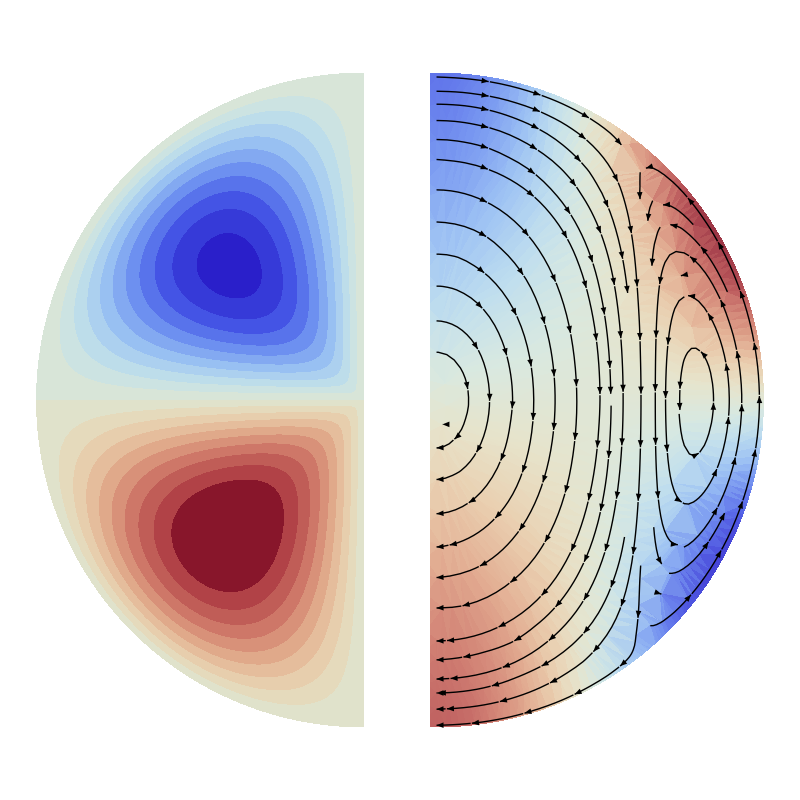

```mathematica
GraphicsGrid[{{
Show[MeridPlot[-gridr,gridθ,gridbr,0,AspectRatio->2,PlotRangePadding->None,Frame->False,Contours->20,PlotRange->All,ContourStyle->None,RegionFunction->Function[{x,y,z},First[Fennec`domain]<Norm[{x,y}]<Last[Fennec`domain]]],PlotLabel->MaTeX["\\text{Radial magnetic field}",Magnification->1]],
Show[StreamMeridPlot[gridr,gridθ,0,{griduρ,griduz,griduϕ},AspectRatio->2,PlotRangePadding->None,Frame->False,PlotRange->All,StreamScale->Medium,StreamStyle->Black,RegionFunction->Function[{x,y,z},First[Fennec`domain]<Norm[{x,y}]<Last[Fennec`domain]]],PlotLabel->MaTeX["\\text{Velocity}",Magnification->1]]}},PlotLabel->MaTeX["\\omega="<>ToString[ω/.(*parameters*)ω->Chop@N[eig⟦pos⟧,5]],Magnification->1.5],Spacings->0]
```

```mathematica
With[{ℓ=4,𝓂=1},
sol=NSolve[(1-σ^2)D[LegendreP[ℓ,𝓂,σ], σ]==𝓂 LegendreP[ℓ,𝓂,σ],σ];
2σ /. sol
]
```

{1.70802,-0.820009,0.611985}

```mathematica
With[{ωin=0.6119849358465923,Le2=0.01,𝓂=1},
{ωin/2(1+√(1+(4𝓂(𝓂+ωin )Le2)/ωin^2)),ωin/2(1-√(1+(4𝓂(𝓂+ωin )Le2)/ωin^2))}
]
```

{0.63728,-0.0252948}